```mathematica
r=2*M*ProductLog[Exp[x/(2*M)-1]]+2*M
```

1.+1. ProductLog[ⅇ^(-1+1. x)]

```mathematica
M=0.5
```

0.5

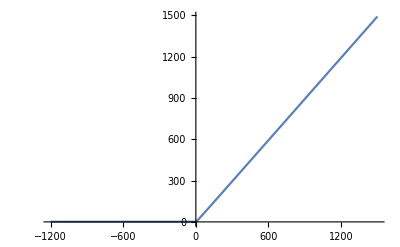

```mathematica
Plot[r,{x,-1200,1500}]
```

```mathematica
rx=Table[r,{x,-1000,1000,0.01}];
```

```mathematica
Export["/Users/alexkemp/Desktop/Grav wave lit/GW-code-GIT/r_of_x.mat",rx]
```

/Users/alexkemp/Desktop/Grav wave lit/GW-code-GIT/r_of_x.mat

```mathematica
Dimensions[rx]
```

{20001}